```mathematica
(* 
Quantities:
   l: orbital angular momentum magnitude
  s: stellar spin angular momentum magnitude
t: total angular momentum magnitude
*)
```

```mathematica
(* Cos[θ] in order to ensure total angular momentum is conserved *)
c[s_,l_,t_]:=(t^2 - l^2 - s^2)/(2*s*l)
```

```mathematica
(* rate of evolution for stellar angular momentum if only the m = 1, m' = 0 term is active, with an overall factor of (3π)/5 Subscript[T, 0] Subscript[Δ, 10] removed *)
Clear[s,l,t]
f10[s_,l_,t_]=FullSimplify[c[s,l,t]^2*(1 - c[s,l,t]^2),Assumptions->{t≤l+s,t≥l-s,t>0,t>l,t>s,s>0,l>0,l>s}]
```

-((l-s-t) (l+s-t) (l-s+t) (l+s+t) (l^2+s^2-t^2)^2)/(16 l^4 s^4)

```mathematica
(* rate of evolution for stellar angular momentum if only the m = 1, m' = 0 term is active, with an overall factor of (3π)/5 Subscript[T, 0] Subscript[Δ, 10] removed *)
Clear[s,l,t]
f20[s_,l_,t_]=FullSimplify[(1 - c[s,l,t]^2)^2,Assumptions->{t≤l+s,t≥l-s,t>0,t>l,t>s,s>0,l>0,l>s}]
```

(1-((l^2+s^2-t^2)^2)/(4 l^2 s^2))^2

```mathematica
FullSimplify[D[f10[s, l, t], s]]
```

((l^2-s^2-t^2) (l^2+s^2-t^2) (l^4+s^4-2 (l^2+s^2) t^2+t^4))/(4 l^4 s^5)

```mathematica
lindecay10[s_,l_,t_]=FullSimplify[Integrate[1/f10[s,l,t], s],Assumptions->{t≤l+s,l≤t+s,s≤t+l,t>0,t>l,t>s,s>0,l>0,l>s}]
```

l (-(2 l s)/(l^2+s^2-t^2)+(-1+l/t) ArcTanh[(-l+t)/s]+((l+t) ArcTanh[(l+t)/s])/t-(2 l ArcTanh[s/(√(-l^2+t^2))])/(√(-l^2+t^2)))

```mathematica
lindecay20[s_,l_,t_]=FullSimplify[Integrate[1/f20[s,l,t], s],Assumptions->{t≤l+s,l≤t+s,s≤t+l,t>0,t>l,t>s,s>0,l>0,l>s}]
```

(l ((2 l s t (l^4-s^2 t^2+t^4-l^2 (s^2+2 t^2)))/(l^4+(s^2-t^2)^2-2 l^2 (s^2+t^2))+(-l^3+t^3) ArcTanh[s/(l-t)]+(l^3+t^3) ArcTanh[s/(l+t)]))/(2 t^3)

```mathematica
FullSimplify[Re[ArcTanh[x]]-Log[1+x]/2+Log[x-1]/2,Assumptions->{x>1}]
```

0

```mathematica
sfunc10[s_,l_,t_,si_]=Simplify[lindecay10[s,l,t]-lindecay10[si,l,t],Assumptions->{t≤(l+s),t>l,t>s,t>0,s>0,l>0,si>0,s<si}]
```

l (-(2 l s)/(l^2+s^2-t^2)+(2 l si)/(l^2+si^2-t^2)+((l-t) ArcTanh[(l-t)/si])/t+(-1+l/t) ArcTanh[(-l+t)/s]+((l+t) ArcTanh[(l+t)/s])/t-((l+t) ArcTanh[(l+t)/si])/t-(2 l ArcTanh[s/(√(-l^2+t^2))])/(√(-l^2+t^2))+(2 l ArcTanh[si/(√(-l^2+t^2))])/(√(-l^2+t^2)))

```mathematica
sfunc20[s_,l_,t_,si_]=Simplify[lindecay20[s,l,t]-lindecay20[si,l,t],Assumptions->{t≤(l+s),t>l,t>s,t>0,s>0,l>0,si>0,s<si}]
```

(l ((2 l s t (l^4-s^2 t^2+t^4-l^2 (s^2+2 t^2)))/(l^4+(s^2-t^2)^2-2 l^2 (s^2+t^2))-(2 l si t (l^4-si^2 t^2+t^4-l^2 (si^2+2 t^2)))/(l^4+(si^2-t^2)^2-2 l^2 (si^2+t^2))+(-l^3+t^3) ArcTanh[s/(l-t)]+(l^3-t^3) ArcTanh[si/(l-t)]+(l^3+t^3) ArcTanh[s/(l+t)]-(l^3+t^3) ArcTanh[si/(l+t)]))/(2 t^3)

```mathematica
FullSimplify[%12]
```

(l ((2 l s t (l^4-s^2 t^2+t^4-l^2 (s^2+2 t^2)))/(l^4+(s^2-t^2)^2-2 l^2 (s^2+t^2))-(2 l si t (l^4-si^2 t^2+t^4-l^2 (si^2+2 t^2)))/(l^4+(si^2-t^2)^2-2 l^2 (si^2+t^2))+(-l^3+t^3) ArcTanh[s/(l-t)]+(l^3-t^3) ArcTanh[si/(l-t)]+(l^3+t^3) ArcTanh[s/(l+t)]-(l^3+t^3) ArcTanh[si/(l+t)]))/(2 t^3)

```mathematica
For[
s=0.05,
s<=0.1,
s+=0.01,
Print["L_10(", s * π, ")=",sfunc10[s,1,1.05,0.1]*π]
]
```

L_10(0.15708)=-3.11131+0.234991 ⅈ

L_10(0.188496)=-0.577962-1.39515×10^-15 ⅈ

L_10(0.219911)=-0.447542-1.39515×10^-15 ⅈ

L_10(0.251327)=-0.31774-1.39515×10^-15 ⅈ

L_10(0.282743)=-0.171561-1.39515×10^-15 ⅈ

L_10(0.314159)=1.41695×10^-15-1.39515×10^-15 ⅈ

```mathematica
For[
s=0.05,
s<=0.050001,
s+=0.0000001,
Print["L_20(", s * π, ")=",sfunc20[s,1,1.05,0.1]*π]
]
```

Power::infy: Infinite expression 1/0. encountered.

L_20(0.15708)=ComplexInfinity

L_20(0.15708)=-17811.+0. ⅈ

L_20(0.15708)=-8906.14+0. ⅈ

L_20(0.157081)=-5937.85+0. ⅈ

L_20(0.157081)=-4453.7+0. ⅈ

L_20(0.157081)=-3563.2+0. ⅈ

L_20(0.157082)=-2969.53+0. ⅈ

L_20(0.157082)=-2545.48+0. ⅈ

L_20(0.157082)=-2227.44+0. ⅈ

L_20(0.157082)=-1980.07+0. ⅈ

L_20(0.157083)=-1782.18+0. ⅈ

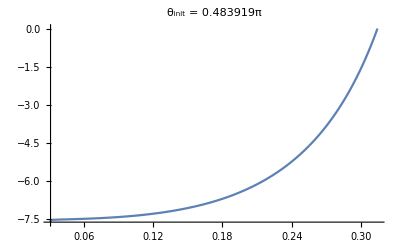

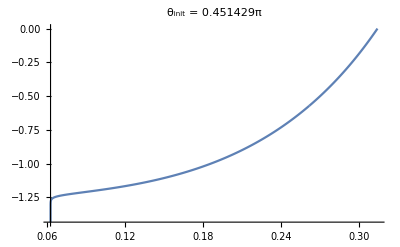

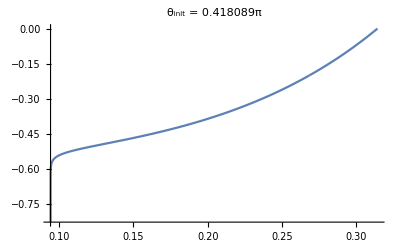

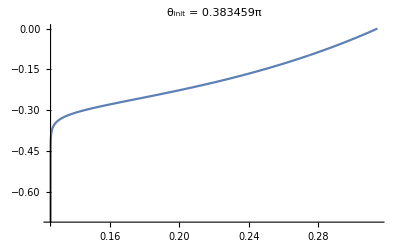

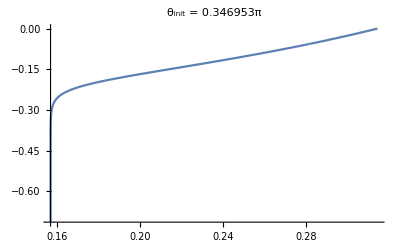

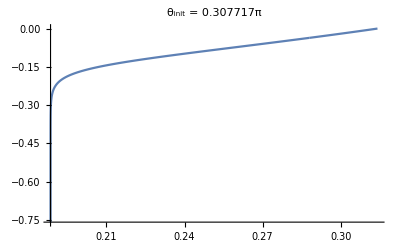

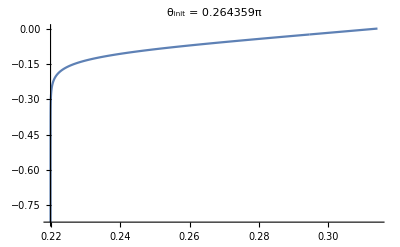

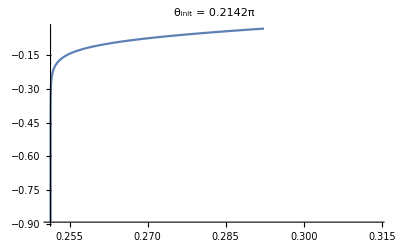

```mathematica
l=π;
sinit = 0.1 * l;
For[
t=1.01 * l,
t<1.1 *l,
t+=0.01 * l,
Plot[sfunc10[s,l,t,sinit]/l, {s,t-l,sinit},PlotPoints->10000,PlotRange->Full, PlotLabel->("θ_init = " <>ToString[ArcCos[(t^2 -l^2 - sinit^2)/(2*sinit*l)]/π]<>"π")]//Print
]
```

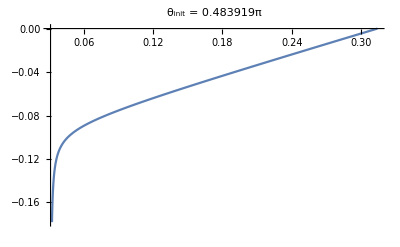

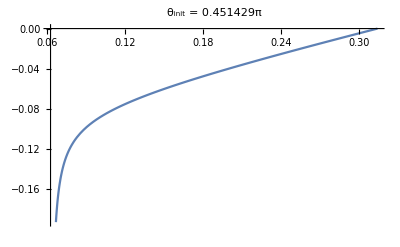

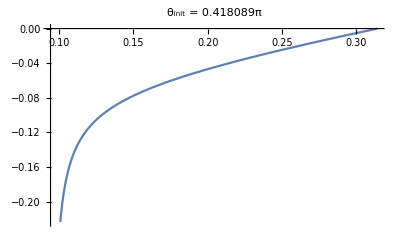

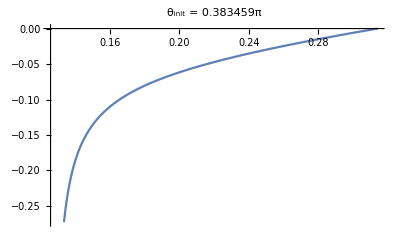

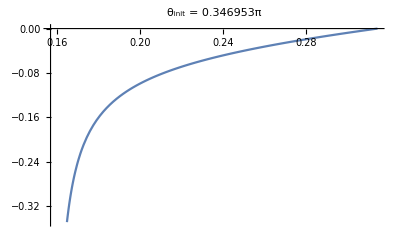

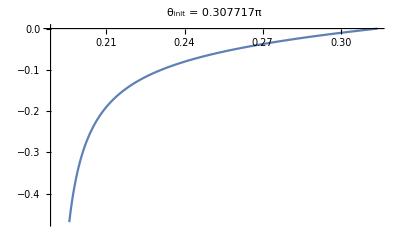

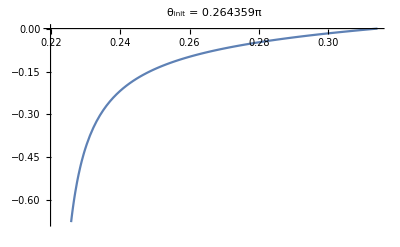

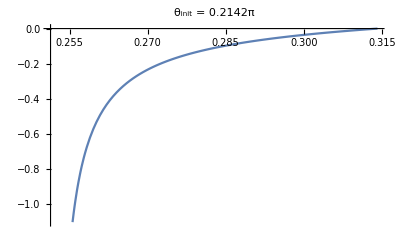

```mathematica
l=π;
sinit = 0.1 * l;
For[
t=1.01 * l,
t<1.1 *l,
t+=0.01 * l,
Plot[sfunc20[s,l,t,sinit]/l, {s,t-l,sinit},PlotPoints->100, PlotLabel->("θ_init = " <>ToString[ArcCos[(t^2 -l^2 - sinit^2)/(2*sinit*l)]/π]<>"π")]//Print
]
```

```mathematica
(*
Given an evolution of the obliquity and spin of the convective zone, angular momentum conservation determines the evolution of the obliquity of the radiative zone if the core and the envelope are completely decoupled and the core is non-dissipative.
*) 
FullSimplify[Solve[l Sin[δ] + s Sin[θ + δ] == si, δ]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{δ→-1. ArcCos[(9.09091 si Sin[θ]-0.00413223 √(3.91309×10^10-3.95268×10^9 si^2+(5.46296×10^9-2.7646×10^8 si^2) Cos[θ]+1.19451×10^8 Cos[2 θ]+836292. Cos[3 θ]+4.84×10^6 si^2 Sin[θ]^2))/(816.67+57.1199 Cos[θ])]},{δ→ArcCos[(9.09091 si Sin[θ]-0.00413223 √(3.91309×10^10-3.95268×10^9 si^2+(5.46296×10^9-2.7646×10^8 si^2) Cos[θ]+1.19451×10^8 Cos[2 θ]+836292. Cos[3 θ]+4.84×10^6 si^2 Sin[θ]^2))/(816.67+57.1199 Cos[θ])]},{δ→-1. ArcCos[(9.09091 si Sin[θ]+0.00413223 √(3.91309×10^10-3.95268×10^9 si^2+(5.46296×10^9-2.7646×10^8 si^2) Cos[θ]+1.19451×10^8 Cos[2 θ]+836292. Cos[3 θ]+4.84×10^6 si^2 Sin[θ]^2))/(816.67+57.1199 Cos[θ])]},{δ→ArcCos[(9.09091 si Sin[θ]+0.00413223 √(3.91309×10^10-3.95268×10^9 si^2+(5.46296×10^9-2.7646×10^8 si^2) Cos[θ]+1.19451×10^8 Cos[2 θ]+836292. Cos[3 θ]+4.84×10^6 si^2 Sin[θ]^2))/(816.67+57.1199 Cos[θ])]}}

```mathematica
{{δ->-ArcCos[(-√((l+s Cos[θ])^2 (l^2+s^2-si^2+2 l s Cos[θ]))+s si Sin[θ])/(l^2+s^2+2 l s Cos[θ])]},{δ->ArcCos[(-√((l+s Cos[θ])^2 (l^2+s^2-si^2+2 l s Cos[θ]))+s si Sin[θ])/(l^2+s^2+2 l s Cos[θ])]},	{δ->-ArcCos[(√((l+s Cos[θ])^2 (l^2+s^2-si^2+2 l s Cos[θ]))+s si Sin[θ])/(l^2+s^2+2 l s Cos[θ])]},{δ->ArcCos[(√((l+s Cos[θ])^2 (l^2+s^2-si^2+2 l s Cos[θ]))+s si Sin[θ])/(l^2+s^2+2 l s Cos[θ])]}}
```